```mathematica
ParabolaArcLength[a_,l_]=Refine[Integrate[√(1.+(2. a x)^2),{x,-l/2.,l/2.}],{a>0.,l>0.}];
ParabolaLowerArea[a_,l_]=Integrate[a x^2,{x,-l/2.,l/2.}];
Res[h_,a_,L_]=1/Simplify[Integrate[1/(h+a(L/2)^2-a(l-L/2)^2)/L,{l,0,L}],{h>0,a>0,L>0}];
```

```mathematica
ParabolaUpperArea[a_,l_]:=l a (l/2.)^2-ParabolaLowerArea[a,l]
Clear[ParabolaWidth]
ParabolaWidth[W_?NumericQ,a_?NumericQ]:=l/.FindRoot[W==ParabolaArcLength[a,l],{l,W/10.}]
ParabolaArea[W_,a_]:=ParabolaUpperArea[a,ParabolaWidth[W,a]]
ParabolaAverage[W_,a_]=Integrate[a x^2,{x,-W/2,W/2}]/W;
ParabolaOptimizedArea[W_]:=Maximize[ParabolaArea[W,a],a][[1]]
```

```mathematica
TotalArea[H_?NumericQ,W_?NumericQ]:=Maximize[H *ParabolaWidth[W,a] +2 ParabolaArea[W,a],a]
ParabolaA[H_,W_]:=TotalArea[H,W][[2,1,2]]
ParabolaHeight[H_,W_]:=ParabolaA[H,W]*(ParabolaWidth[W,ParabolaA[H,W]]/2)^2
```

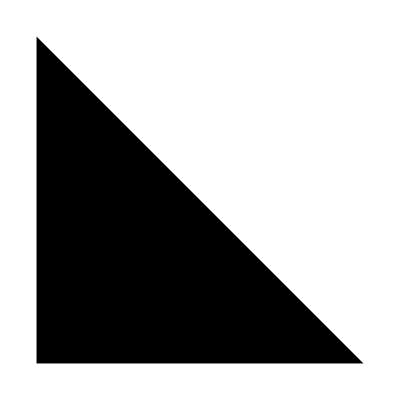

```mathematica
Baffle[H_,W_]=Polygon[{{1,2},{2,1},{1,1}}];
Show[Graphics[Baffle[3,4]]]
```

```mathematica
h=2;
w=6;
ParabolaWidth[w,ParabolaA[h,w]]
ParabolaArea[h,ParabolaA[h,w]]
TotalArea[h,w][[1]]/(h*w)
ParabolaHeight[h,w]
ParabolaAverage[w,ParabolaA[h,w]]
```

4.80587

0.325864

1.6628

1.61395

0.838543

```mathematica
ParabolaAverage[W,a]=Integrate[a x^2,{x,-W/2,W/2}]/W
```

(a W^2)/12

```mathematica
FindRoot[2.5*5==TotalArea[hh,5][[1]],{hh,5}]
ResHW[H_,W_]:=Res[H,ParabolaA[H,W],ParabolaWidth[W,ParabolaA[H,W]]]
ResHW[2.136,2.5]/Res[2.5,0.0001,2.5]
TotalArea[12.5,5][[1]]
```

{hh→12.5}

0.980935

64.0833

{4.66772,{a→0.376393}}

2.69845

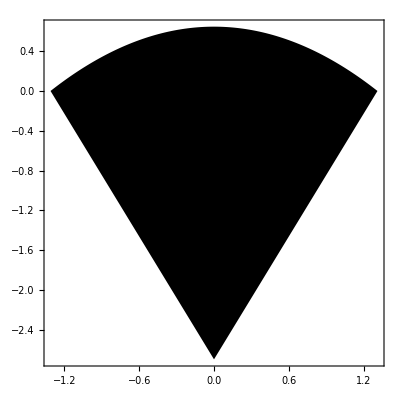

```mathematica
faceLength=3;
baffleLength=3;
TriangleHeight[face_?NumericQ,baffle_?NumericQ,a_]:=Sqrt[baffle^2 -(ParabolaWidth[face,a]/2)^2]
TotalAreaTriangle[face_?NumericQ,baffle_?NumericQ]:=Maximize[Sqrt[baffle^2 -(ParabolaWidth[face,a]/2)^2]*ParabolaWidth[face,a]/2 +ParabolaArea[face,a],a]
area=TotalAreaTriangle[faceLength,baffleLength]
ParabolaArea[faceLength,area[[2,1,2]]];
W=ParabolaWidth[faceLength,area[[2,1,2]]];
h=TriangleHeight[faceLength,baffleLength,area[[2,1,2]]]
parabolaPts=Table[{x,-area[[2,1,2]]*x^2+area[[2,1,2]]*(W/2)^2},{x,-W/2,W/2,W/100}];
baffle=Polygon[Join[parabolaPts,{{0,-h}}]];
Show[{Graphics[baffle,Frame->True,AspectRatio->Automatic]}]
```

```mathematica
N[66*80/36/36]
```

4.07407

```mathematica
2.5*2.5
```

6.25